# Pipeline Quantum

## Embeddings + Classification

Mathematica has a good quantum framework 💃
	https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/
	Play with it, and the YouTube videos
Binary string mapping
        - Big-Endian (normal) - Mathematica: Left-to-right, most significant bit first
        - Little-Endian (abnormal) - Python: Right-to-left, least significant bit first

## Introduction

### Network Parameters

```mathematica
(* Parameters *)
n = 2; (* Number of qubits for |j⟩ *)
m = 1; (* Number of qubits for |k⟩ *)
p = n; (* Precision level *)

(* Derived quantities *)
nrNodes = 2^n; (* Number of nodes *)
s = 2^m; (* Sparsity level *)
P = 2^p; (* Scaling factor *)

(* Initialize adjacency matrix *)
A = ConstantArray[0, {nrNodes, nrNodes}];

(* Circulant graph shifts *)
shifts = If[s <= 2,
   {1, -1},
   Join[Range[1, s/2], -Range[1, s/2]]
];

(* Build adjacency list and adjacency matrix *)
adjacencyList = Table[
   Module[{vList = Mod[i + shifts, nrNodes, 1]},
    (* Update adjacency matrix *)
    Scan[(A[[i, #]] = 1; A[[#, i]] = 1) &, vList];
    vList
    ],
   {i, 1, nrNodes}
];

(* Display adjacency matrix *)
Print["Adjacency Matrix (Sparse):"];
MatrixForm[A]

(* Display adjacency list *)
Print["Adjacency List:"];
adjacencyList

(* Node degrees and squared degrees *)
nodeDegrees = Length /@ adjacencyList;
nodeDegreesC1 = nodeDegrees^2;
Print["Node degrees: ", nodeDegrees];
Print["Node degrees squared: ", nodeDegreesC1];

(* Feature vector (descending from 1 - 1/P to 0) *)
features = N[Round[Subdivide[1 - 1/P, 0, nrNodes - 1], 0.0000000001]];
featuresInt = Round[features * P];
Print["Feature Vector (real): ", features];
Print["Feature Vector (scaled by P): ", featuresInt];
```

Node degrees: {2,2,2,2}

Node degrees squared: {4,4,4,4}

Feature Vector (real): {0.75,0.5,0.25,0.}

Adjacency Matrix (Sparse):

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

Adjacency List:

{{2,4},{3,1},{4,2},{1,3}}

Node degrees: {2,2,2,2}

Node degrees squared: {4,4,4,4}

Feature Vector (real): {0.75,0.5,0.25,0.}

Feature Vector (scaled by P): {3,2,1,0}

Feature Vector (scaled by P): {3,2,1,0}

#### Train/Test Set Details

```mathematica
thClass = 0.75;
classLabels = If[# < thClass, 0, 1] & /@ features;

Print["Class labels: ", classLabels];
Print["Features: ", features];

testNode = 1; (* 1 in Mathematica. 0 in Python. *)
```

Class labels: {1,0,0,0}

Features: {0.75,0.5,0.25,0.}

### Circuit Definitions

#### Dimensions and Gates

```mathematica
(*--------------------------------------- Dimensions for each register ---------------------------------------*)

dimA = 2^5;
dimZ = 2^p;
dimK = 2^(2*m);
dimU2 = 2^n;
dimU1 = 2^n;
dimL2 = 2^m;
dimL1 = 2^m;
dimC = 2^1;
dimI = 2^2;
dimV = 2^n;

(* number of qubits: QuantumCircuit(qr_a, qr_z, qr_k, qr_u2, qr_u1, qr_l2, qr_l1, qr_c, qr_i, qr_v) *)
fullDim = dimA * dimZ * dimK * dimU2 * dimU1 * dimL2 * dimL1 * dimC * dimI * dimV;

idA = IdentityMatrix[dimA];
idZ = IdentityMatrix[dimZ];
idK = IdentityMatrix[dimK];
idU2 = IdentityMatrix[dimU2];
idU1 = IdentityMatrix[dimU1];
idL2 = IdentityMatrix[dimL2];
idL1 = IdentityMatrix[dimL1];
idC = IdentityMatrix[dimC];
idI = IdentityMatrix[dimI];
idV = IdentityMatrix[dimV];

(*--------------------------------------- Hadamard Matrices ---------------------------------------*)

H = (1/Sqrt[2]) * {{1, 1}, {1, -1}};
Hv = KroneckerProduct @@ Table[H, {n}]; (* size: 2^n × 2^n. Apply Kronecker product to a list of H repeated n times. *)
Hl = H;
Hi = KroneckerProduct @@ Table[H, {2}];
Hc = H;
```

#### Oracle O_Y

```mathematica
(* Total number of basis states: 1 (y) + n (v) *)
dimYV = 2^(1 + n);
OY = IdentityMatrix[dimYV];

(* Apply X (Pauli-X) on y, controlled on v = vIndex where y_v = 1 *)
Do[
  If[classLabels[[v]] == 1,
    (* Get binary string of v (0-based) *)
    ctrlBits = IntegerDigits[v - 1, 2, n];
    
    (* Flip y when ctrlBits == v and y == 0 *)
    index0 = FromDigits[Join[ctrlBits, {0}], 2] + 1;
    index1 = FromDigits[Join[ctrlBits, {1}], 2] + 1;
    
    (* Swap the two rows (flip y) *)
    O_Y[[{index0, index1}]] = O_Y[[{index1, index0}]];
  ],
  {v, 1, 2^n}
];
```

### Visualize Bar Chart

```mathematica
createLabels[nrQubitsCurrent_] := 
  StringJoin["|", #, "⟩"] & /@ IntegerString[Range[0, 2^nrQubitsCurrent - 1], 2, nrQubitsCurrent]
	
createBarChart[stateCurrent_] := Module[
  {nrQubitsCurrent = Log2[Length[stateCurrent]], labels},
  labels = createLabels[nrQubitsCurrent];
  BarChart[
    Abs[Normal[stateCurrent]]^2,
    ChartLabels -> labels,
    AxesLabel -> {"Basis state", "Probability"},
    ChartStyle -> "Rainbow",
    ImageSize -> Large
  ]
]
```

# Option 1: Sub-Vector of Interest

Step-by-step classical matrix analogue  (i.e., Kronecker product, explicit vector/matrix constructions, etc.) of each quantum operation. 🕺

## QMME Circuit

## Initialization and Superpositions

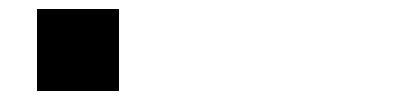

{1/2,1/2,1/2,1/2}

```mathematica
(*--------------------------------------- 0. Initialization ---------------------------------------*)
psiv0 = SparseArray[{1 -> 1}, {dimV}]; (* only the 0th entry is 1, rest are 0 *)
ArrayPlot[Normal[psiv0] // List]

(*--------------------------------------- 1. Hadamard on v ---------------------------------------*)

psiv1 = Hv . psiv0 (* [qr_v] *)
```

## Amplitude Encoding

Here, omit registers qr_a, qr_z, qr_k, qr_u2, qr_u1, qr_l2, qr_l1, and include registers qr_c, qr_i, qr_v.

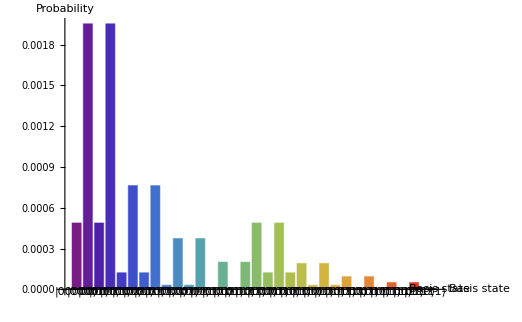

```mathematica
(*--------------------------------------- Feature Encoding ---------------------------------------*)

psix = Transpose[Table[
	(features^i) * psiv1 / (2 * Sqrt[2]) ,  (* element-wise multiply features by i, then multiply by psiv1. *)
	{i, 1, 4}
]]; (* Matrix of dimension N x 4. Each element is psix[v][i]. *)

(*--------------------------------------- Neighbors ---------------------------------------*)

psic0 = (A/s) . psix; (* Analogue with Hadamard on l1 and oracle O_L, on top of node itself -> sum of first-neighbors features *)
psic1 = (A/s) . psic0; (* Analogue with Hadamard on l2 and oracle O_L, on top on first-neighbors -> sum of second-neighbors features *)

(*--------------------------------------- Division by number of neighbors ---------------------------------------*)

psikc0 = Flatten[Transpose[DiagonalMatrix[1/nodeDegrees].psic0]]; (* Transpose and Flatten lead to[i=1, v=1][i=1, v=2] etc. *)
psikc1 = Flatten[Transpose[DiagonalMatrix[1/nodeDegreesC1].psic1]];

(*--------------------------------------- 8 Features of Interest ---------------------------------------*)

(* 1st qubit for c, next 2 qubits for i, and next qubits for v. *)
psiInterest = Join[psikc0, psikc1]; (* Vector of dimension 8 x nrNodes. *)

createBarChart[psiInterest]
```

## Classifier Circuit

## State Preparation

### Test Features Encoding

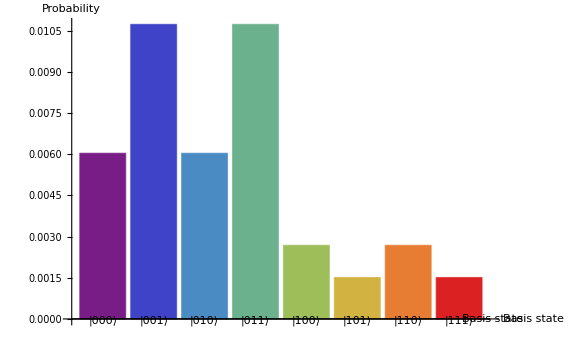

```mathematica
(*--------------------------------------- Test Features Encoding ---------------------------------------*)

psiTestx = Table[
  (features[[testNode]]^i) / (2 * Sqrt[2]),
  {i, 1, 4}
];

psiTestc0 = (A/s) . psiTestx; (* Analogue with Hadamard on l1 and oracle O_L, on top of node itself -> sum of first-neighbors features *)
psiTestc1 = (A/s) . psiTestc0; (* Analogue with Hadamard on l2 and oracle O_L, on top on first-neighbors -> sum of second-neighbors features *)

(* Simpler Division by Number of Neighbors *)
psiTestkc0 = 1/nodeDegrees[[testNode]] * psiTestc0; 
psiTestkc1 = 1/nodeDegreesC1[[testNode]] * psiTestc1;

(* 1st qubit for c, next 2 qubits for i. *)
psiTestInterest = Join[psiTestkc0, psiTestkc1]; (* Vector of dimension 8*)

createBarChart[psiTestInterest]
```

### Test/Train Data Combined (ONGOING)

```mathematica
psiY = {1, 0};
psiCombo = KroneckerProduct[psiTestInterest, psiInterest, psiY] // Flatten;

(* Positions of v and y: last n+1 qubits *)
nrQubitsOY = Log2[Length[psiCombo]]
targetPositions = Range[nrQubitsOY - n, nrQubitsOY];

(* Apply partial unitary *)
ApplyPartialUnitary[state_, U_, targets_, total_] := Module[
  {dims = ConstantArray[2, total]},
  TensorProductOperator[dims, U, targets] . state
];

psiPrepared = ApplyPartialUnitary[psiCombo, OY, targetPositions, totalQubits];
```

9

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[2,totalQubits].

## Swap-Test Classifier

# Option 2: Replicating the Circuit with Full Vector

## QMME Circuit

## Initialization and Superpositions

```mathematica
(*--------------------------------------- 0. Initialization ---------------------------------------*)

(* Initial state all zeros *)
initState = SparseArray[{1 -> 1}, {fullDim}];

(*--------------------------------------- 1. and 2. Hadamard on v and l1 ---------------------------------------*)

firstH = KroneckerProduct[ 
   idA, idZ, idK, idU2, idU1, idL2, idL1,
   Hm,
   idC, idI,
   Hv
]; (* Full operator: Apply H on qr_v and qr_l1 only, identity elsewhere *)

stateAfterH = fullH . initState;
```

# The End